```mathematica
Clear["Global`*"]
(* =================================================================*)
(*第一部分：系统定义*)
(* =================================================================*)

(*定义二阶离散线性系统 x(k+1)=A*x(k)+B*u(k)*)
matrixA=({{1.0, 1.0}, {0.0, 1.0}});
matrixB=({{0}, {1.0}});
matrixC=({{1, 0}, {0, 1}});

(*系统维度*)
nx=2; (*状态维度*)
nu=1; (*输入维度*)
ny=2; (*输出维度*)

Print["系统矩阵 A = ",MatrixForm[matrixA]];
Print["输入矩阵 B = ",MatrixForm[matrixB]];
Print["输出矩阵 C = ",MatrixForm[matrixC]];

(*检查系统稳定性*)
eigenVals=Eigenvalues[matrixA];
Print["系统特征值: ",eigenVals];
isStable=Max[Abs[eigenVals]]<1;
Print["系统稳定性: ",If[isStable,"稳定","不稳定"]];
```

系统矩阵 A = (1. | 1.
0. | 1.)

输入矩阵 B = (0
1.)

输出矩阵 C = (1 | 0
0 | 1)

系统特征值: {1.,1.}

系统稳定性: 不稳定

```mathematica
(* =================================================================*)
(*第二部分：MPC参数设置*)
(* =================================================================*)

(*MPC参数*)
Np=20; (*预测步长*)
Nc=10;  (*控制步长*)

(*权重矩阵*)
Q={{1,0},{0,1}};  (*状态权重矩阵*)
R={{100}};               (*控制权重矩阵*)
S={{1000,0},{0,1000}}; (*终端权重矩阵*)

(*约束*)
uMin=-0.3;
uMax=0.3;

Print["预测步长 Np = ",Np];
Print["控制步长 Nc = ",Nc];
Print["状态权重矩阵 Q = ",MatrixForm[Q]];
Print["控制权重矩阵 R = ",MatrixForm[R]];
```

预测步长 Np = 20

控制步长 Nc = 10

状态权重矩阵 Q = (1 | 0
0 | 1)

控制权重矩阵 R = (100)

```mathematica
(* =================================================================*)
(*第三部分：构建MPC预测模型*)
(* =================================================================*)

(*构建预测矩阵 F*)
(*F 是 (Np*nx) x nx 的矩阵*)
F=Flatten[Table[MatrixPower[matrixA,i],{i,1,Np}],1];

Print["预测矩阵 F 的维度: ",Dimensions[F]];

(*构建控制矩阵 G*)
(*G 是 (Np*nx) x (Nc*nu) 的矩阵*)
G=Table[0,{Np*nx},{Nc*nu}];
For[i=1,i<=Np,i++,For[j=1,j<=Nc,j++,If[j<=i,(*计算 A^(i-j)*B*)AiB=If[i==j,matrixB,MatrixPower[matrixA,i-j].matrixB];
For[row=1,row<=nx,row++,For[col=1,col<=nu,col++,G[[(i-1)*nx+row,(j-1)*nu+col]]=AiB[[row,col]];];];];];];

Print["控制矩阵 G 的维度: ",Dimensions[G]];
```

预测矩阵 F 的维度: {40,2}

控制矩阵 G 的维度: {40,10}

```mathematica
(* =================================================================*)
(*第四部分：构建权重矩阵*)
(* =================================================================*)

(*构建状态权重矩阵 Qbar*)
Qbar=Table[0,{Np*nx},{Np*nx}];
For[i=1,i<=Np,i++,weightMatrix=If[i==Np,S,Q];
For[j=1,j<=nx,j++,For[k=1,k<=nx,k++,Qbar[[(i-1)*nx+j,(i-1)*nx+k]]=weightMatrix[[j,k]];];];];

(*构建控制权重矩阵 Rbar*)
Rbar=KroneckerProduct[IdentityMatrix[Nc],R];

(*计算 Hessian 矩阵*)
H=Transpose[G].Qbar.G+Rbar;
Print["Hessian矩阵维度: ",Dimensions[H]];
```

Hessian矩阵维度: {10,10}

```mathematica
(* =================================================================*)
(*第五部分：使用LinearProgramming的替代方案*)
(* =================================================================*)

(*由于QuadraticOptimization可能有问题，我们使用数值方法*)
solveMPCNumerical[x0_]:=Module[{f,constraintMat,constraintVec,result},(*计算线性项*)f=Transpose[G].Qbar.F.x0;
(*构建约束矩阵 (简化版本，只考虑控制约束)*)constraintMat=Join[IdentityMatrix[Nc*nu],(*u<=uMax*)-IdentityMatrix[Nc*nu]    (*u>=uMin*)];
constraintVec=Join[Table[uMax,{Nc*nu}],(*上界约束*)Table[-uMin,{Nc*nu}]     (*下界约束*)];

(*使用数值优化*)result=NMinimize[{0.5*Table[u[i],{i,1,Nc*nu}].H
.Table[u[i],{i,1,Nc*nu}]+f.Table[u[i],{i,1,Nc*nu}],(*约束条件*)Table[uMin<=u[i]<=uMax,{i,1,Nc*nu}]},Table[u[i],{i,1,Nc*nu}]];
(*提取第一个控制量*)u[1]/. result[[2]]];
```

```mathematica
(* =================================================================*)
(*第六部分：更简单的分析解法*)
(* =================================================================*)

(*对于无约束情况，我们可以得到解析解*)
solveMPCAnalytical[x0_]:=Module[{f,optimalU},(*计算线性项*)f=Transpose[G].Qbar.F.x0;
(*无约束解析解:U* =-H^(-1)*f*)optimalU=-Inverse[H].f;
(*应用约束*)optimalU=Map[Clip[#,{uMin,uMax}]&,optimalU];

(*返回第一个控制量*)optimalU[[1]]];
```

开始MPC仿真...

初始状态: {10,0}

步数 5: 状态 = {7.,-1.32}, 控制 = -0.122

步数 10: 状态 = {1.46,-0.607}, 控制 = 0.183

步数 15: 状态 = {-0.205,-0.0522}, 控制 = 0.0609

步数 20: 状态 = {-0.183,0.0383}, 控制 = 0.000872

步数 25: 状态 = {-0.0326,0.0151}, 控制 = -0.00504

步数 30: 状态 = {0.00693,0.000815}, 控制 = -0.00146

仿真完成！

最终状态: {0.00693,0.0008149}

=== 仿真结果 ===

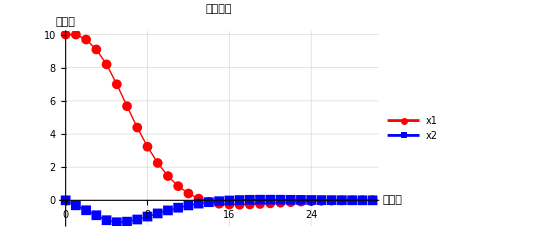

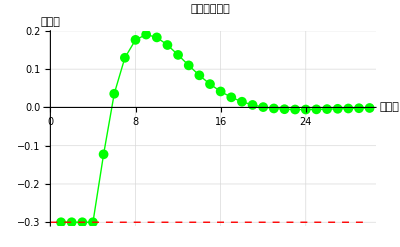

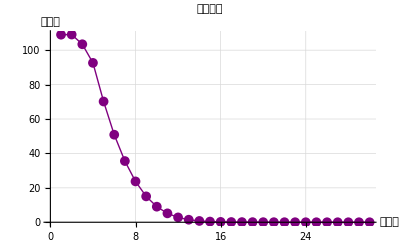

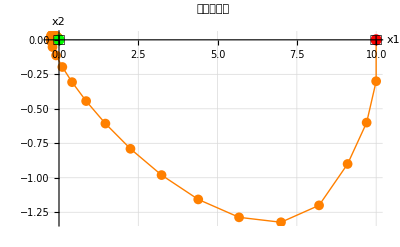

=== 性能指标 ===

最终误差: 0.006978

总代价: 629.9

最大控制量: 0.3

稳定时间: 24

NumberForm::reqsigz: 要求的数字精度低于显示的位数；用零进行填充.

General::stop: 在本次计算中，NumberForm::reqsigz 的进一步输出将被抑制.

Hessian矩阵条件数: LinearAlgebra`MatrixConditionNumber[{{364200.,345000.,325800.,306600.,287500.,268300.,249100.,230000.,210800.,191700.},{345000.,326900.,308600.,290500.,272300.,254200.,236100.,217900.,199800.,181700.},{325800.,308600.,291600.,274400.,257200.,240100.,223000.,205800.,188700.,171600.},{306600.,290500.,274400.,258400.,242100.,226000.,209900.,193800.,177700.,161600.},{287500.,272300.,257200.,242100.,227100.,211900.,196800.,181700.,166600.,151500.},{268300.,254200.,240100.,226000.,211900.,197900.,183700.,169700.,155600.,141500.},{249100.,236100.,223000.,209900.,196800.,183700.,170800.,157600.,144500.,131400.},{230000.,217900.,205800.,193800.,181700.,169700.,157600.,145600.,133500.,121400.},{210800.,199800.,188700.,177700.,166600.,155600.,144500.,133500.,122500.,111300.},{191700.,181700.,171600.,161600.,151500.,141500.,131400.,121400.,111300.,101400.}}]

```mathematica
(* =================================================================*)
(*第七部分：仿真测试*)
(* =================================================================*)

(*初始条件*)
x0={10,0};
simSteps=30;

(*存储数据*)
xHistory={x0};
uHistory={};
costHistory={};

(*当前状态*)
xCurrent=x0;

Print["开始MPC仿真..."];
Print["初始状态: ",xCurrent];

(*仿真循环*)
For[k=1,k<=simSteps,k++,(*求解MPC*)uOpt=solveMPCNumerical[xCurrent];
(*应用控制到系统*)xNext=matrixA.xCurrent+matrixB.{uOpt};
(*计算代价*)cost=xCurrent.Q.xCurrent+uOpt^2*R[[1,1]];
(*存储数据*)AppendTo[xHistory,xNext];
AppendTo[uHistory,uOpt];
AppendTo[costHistory,cost];
(*更新状态*)xCurrent=xNext;
(*显示进度*)If[Mod[k,5]==0,Print["步数 ",k,": 状态 = ",NumberForm[xCurrent,3],", 控制 = ",NumberForm[uOpt,3]]];];

Print["仿真完成！"];
Print["最终状态: ",NumberForm[xCurrent,4]];

(* =================================================================*)
(*第八部分：结果可视化*)
(* =================================================================*)

(*状态轨迹*)
x1Traj=Table[{k-1,xHistory[[k,1]]},{k,1,Length[xHistory]}];
x2Traj=Table[{k-1,xHistory[[k,2]]},{k,1,Length[xHistory]}];

stateTrajectoryPlot=ListLinePlot[{x1Traj,x2Traj},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic,Medium},PlotLabel->"状态轨迹",AxesLabel->{"时间步","状态值"},PlotLegends->{"x1","x2"},GridLines->Automatic,PlotRange->All];

(*控制轨迹*)
controlTraj=Table[{k,uHistory[[k]]},{k,1,Length[uHistory]}];
controlTrajectoryPlot=ListLinePlot[controlTraj,PlotStyle->{Green,Thick},PlotMarkers->{Automatic,Medium},PlotLabel->"控制输入轨迹",AxesLabel->{"时间步","控制值"},GridLines->Automatic,Epilog->{{Red,Dashed,Line[{{0,uMax},{simSteps,uMax}}]},{Red,Dashed,Line[{{0,uMin},{simSteps,uMin}}]}}];

(*代价轨迹*)
costTraj=Table[{k,costHistory[[k]]},{k,1,Length[costHistory]}];
costTrajectoryPlot=ListLinePlot[costTraj,PlotStyle->{Purple,Thick},PlotMarkers->{Automatic,Medium},PlotLabel->"代价函数",AxesLabel->{"时间步","代价值"},GridLines->Automatic];

(*相平面图*)
phaseTraj=Table[{xHistory[[k,1]],xHistory[[k,2]]},{k,1,Length[xHistory]}];
phasePlot=ListLinePlot[phaseTraj,PlotStyle->{Orange,Thick},PlotMarkers->{Automatic,Medium},PlotLabel->"相平面轨迹",AxesLabel->{"x1","x2"},GridLines->Automatic,Epilog->{{Red,PointSize[0.02],Point[{x0[[1]],x0[[2]]}]},{Text["起点",{x0[[1]],x0[[2]]},{0,-1.5}]},{Green,PointSize[0.02],Point[{0,0}]},{Text["目标",{0,0},{0,-1.5}]}}];

(*显示图形*)
Print["=== 仿真结果 ==="];
stateTrajectoryPlot
controlTrajectoryPlot
costTrajectoryPlot
phasePlot

(* =================================================================*)
(*第九部分：性能分析*)
(* =================================================================*)

finalError=Norm[xCurrent];
totalCost=Total[costHistory];
maxControl=Max[Abs[uHistory]];

Print["=== 性能指标 ==="];
Print["最终误差: ",NumberForm[finalError,4]];
Print["总代价: ",NumberForm[totalCost,4]];
Print["最大控制量: ",NumberForm[maxControl,4]];

(*稳定时间计算*)
stateNorms=Table[Norm[xHistory[[k]]],{k,1,Length[xHistory]}];
settlingIndex=FirstPosition[stateNorms,x_/;x<0.1];
Print["稳定时间: ",If[settlingIndex===Missing["NotFound"],"未稳定",settlingIndex[[1]]]];
(*展示矩阵条件数*)
Print["Hessian矩阵条件数: ",NumberForm[LinearAlgebra`MatrixConditionNumber[H],4]];
```